# A Quantum-Like for the International Interaction Game

## The International Interaction Backward Induction Model

Explain here the Signorino  tree based model
-Graphics-

## Classical Approach

```mathematica
(*Set recursion limit to handle complex nested functions*)
$RecursionLimit=10000;
```

```mathematica
(*Define phase parameters globally-ADDED*)
(* θ1=0; *)
(* θ2=0; *)
```

### Backward Induction Functions - Classical Setting

```mathematica
q10cl[U2War1_,U2Cap2_]:=E^U2War1/(E^U2War1+E^U2Cap2);

notq10cl[U2War1_,U2Cap2_]:=1-q10cl[U2War1,U2Cap2];

q11cl[U2War1_,U2Cap2_]:=q10cl[U2War1,U2Cap2];

notq11cl[U2War1_,U2Cap2_]:=notq10cl[U2War1,U2Cap2];

p8cl[U1War2_,U1Cap1_]:=E^U1War2/(E^U1War2+E^U1Cap1);

notp8cl[U1War2_,U1Cap1_]:=1-p8cl[U1War2,U1Cap1];

p12cl[U1War2_,U1Cap1_]:=p8cl[U1War2,U1Cap1];

notp12cl[U1War2_,U1Cap1_]:=notp8cl[U1War2,U1Cap1];

q9cl[U1War2_,U1Cap1_,U2War2_,U2Cap1_,U2Nego_]:=Module[{UP2N12,p12,notp12},
p12=p12cl[U1War2,U1Cap1];
notp12=notp12cl[U1War2,U1Cap1];
UP2N12=p12 U2War2+notp12 U2Cap1;
E^UP2N12/(E^UP2N12+E^U2Nego)];

notq9cl[U1War2_,U1Cap1_,U2War2_,U2Cap1_,U2Nego_]:=1-q9cl[U1War2,U1Cap1,U2War2,U2Cap1,U2Nego];

p7cl[U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_]:=Module[{UP1N11,q11,notq11},q11=q11cl[U2War1,U2Cap2];
notq11=notq11cl[U2War1,U2Cap2];
UP1N11=q11 U1War1+notq11 U1Cap2;
E^UP1N11/(E^UP1N11+E^U1Nego)];

notp7cl[U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_]:=1-p7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];

q6cl[U1War1_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_]:=Module[{UP2N8,U2N11,UP2N7,p8,notp8,p7,notp7,q11,notq11},p8=p8cl[U1War2,U1Cap1];
notp8=notp8cl[U1War2,U1Cap1];
notp7=notp7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
p7=p7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
UP2N8=p8 U2War2+notp8 U2Cap1;
q11=q11cl[U2War1,U2Cap2];
notq11=notq11cl[U2War1,U2Cap2];
U2N11=q11 U2War1+notq11 U2Cap2;
UP2N7=p7 U2N11+notp7 U2Nego;
E^UP2N8/(E^UP2N8+E^UP2N7)];

notq6cl[U1War1_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_]:=1-q6cl[U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

p5cl[U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_]:=Module[{UP1N10,UP2N10,UP2N9,UP1N9,q10,notq10,q9,notq9,p12,notp12,UP1N12},p12=p12cl[U1War2,U1Cap1];
notp12=notp12cl[U1War2,U1Cap1];
UP1N12=p12 U1War2+notp12 U1Cap1;
q10=q10cl[U2War1,U2Cap2];
notq10=notq10cl[U2War1,U2Cap2];
q9=q9cl[U1War2,U1Cap1,U2War2,U2Cap1,U2Nego];
notq9=notq9cl[U1War2,U1Cap1,U2War2,U2Cap1,U2Nego];
UP1N10=q10 U1War1+notq10 U1Cap2;
UP1N9=q9 UP1N12+notq9 U1Nego;
E^UP1N10/(E^UP1N10+E^UP1N9)];

notp5cl[U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_]:=1-p5cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego];

p4cl[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_]:=Module[{UP1N6,q11,notq11,p8,notp8,p7,notp7,q6,notq6,UP1N11,UP1N8,UP1N7},q11=q11cl[U2War1,U2Cap2];
(*CORRECTED:Was incorrectly using notp12cl instead of notq11cl*)
notq11=notq11cl[U2War1,U2Cap2];
p8=p8cl[U1War2,U1Cap1];
notp8=notp8cl[U1War2,U1Cap1];
p7=p7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
notp7=notp7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
q6=q6cl[U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
notq6=notq6cl[U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
UP1N11=q11 U1War1+notq11 U1Cap2;
UP1N8=p8 U1War2+notp8 U1Cap1;
UP1N7=p7 UP1N11+notp7 U1Nego;
UP1N6=q6 UP1N8+notq6 UP1N7;
E^UP1N6/(E^UP1N6+E^U1Acq1)];

notp4cl[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_]:=1-p4cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1];

q3cl[U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,U2Acq2_]:=Module[{UP2N12,UP2N10,UP2N9,UP2N5,p12,notp12,q10,notq10,q9,notq9,p5,notp5},p12=p12cl[U1War2,U1Cap1];
notp12=notp12cl[U1War2,U1Cap1];
UP2N12=p12 U2War2+notp12 U2Cap1;
q10=q10cl[U2War1,U2Cap2];
notq10=notq10cl[U2War1,U2Cap2];
UP2N10=q10 U2War1+notq10 U2Cap2;
q9=q9cl[U1War2,U1Cap1,U2War2,U2Cap1,U2Nego];
notq9=notq9cl[U1War2,U1Cap1,U2War2,U2Cap1,U2Nego];
UP2N9=q9 UP2N12+notq9 U2Nego;
p5=p5cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego];
notp5=notp5cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego];
UP2N5=p5 UP2N10+notp5 UP2N9;
E^UP2N5/(E^UP2N5+E^U2Acq2)];

notq3cl[U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,U2Acq2_]:=1-q3cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2];

q2cl[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_]:=Module[{UP2N4,q11,notq11,p7,notp7,p8,notp8,q6,notq6,p4,notp4,UP2N11,UP2N7,UP2N8,UP2N6},q11=q11cl[U2War1,U2Cap2];
notq11=notq11cl[U2War1,U2Cap2];
p7=p7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
notp7=notp7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
p8=p8cl[U1War2,U1Cap1];
notp8=notp8cl[U1War2,U1Cap1];
q6=q6cl[U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
notq6=notq6cl[U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
p4=p4cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1];
notp4=notp4cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1];
UP2N11=q11 U2War1+notq11 U2Cap2;
UP2N7=p7 UP2N11+notp7 U2Nego;
UP2N8=p8 U2War2+notp8 U2Cap1;
UP2N6=q6 UP2N8+notq6 UP2N7;
UP2N4=p4 UP2N6+notp4 U2Acq1;
E^UP2N4/(E^UP2N4+E^U2SQ)];


notq2cl[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_]:=1-q2cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

p1cl[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:=Module[{UP1N2,UP1N3,UP1N4,UP1N5,UP1N6,UP1N9,UP1N10,UP1N12,q2,notq2,q3,notq3,p4,notp4,p5,notp5,q6,notq6,p8,notp8,p7,notp7,q9,notq9,q10,notq10,q11,notq11,p12,notp12,UP1N11,UP1N7,UP1N8},p12=p12cl[U1War2,U1Cap1];
notp12=notp12cl[U1War2,U1Cap1];
p8=p8cl[U1War2,U1Cap1];
notp8=notp8cl[U1War2,U1Cap1];
q11=q11cl[U2War1,U2Cap2];
notq11=notq11cl[U2War1,U2Cap2];
q10=q10cl[U2War1,U2Cap2];

(*CORRECTED:Was incorrectly using notp12cl instead of notq10cl*)
notq10=notq10cl[U2War1,U2Cap2];

q9=q9cl[U1War2,U1Cap1,U2War2,U2Cap1,U2Nego];
notq9=notq9cl[U1War2,U1Cap1,U2War2,U2Cap1,U2Nego];
p7=p7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
notp7=notp7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
q6=q6cl[U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
notq6=notq6cl[U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
p5=p5cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego];
notp5=notp5cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego];
p4=p4cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1];
notp4=notp4cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1];
q3=q3cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2];
notq3=notq3cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2];
q2=q2cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];
notq2=notq2cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];
UP1N12=p12 U1War1+notp12 U1Cap1;
UP1N11=q11 U1War1+notq11 U1Cap2;
UP1N9=q9 UP1N12+notq9 U1Nego;
UP1N7=p7 UP1N11+notp7 U1Nego;
UP1N8=p8 U2War2+notp8 U2Cap1;
UP1N10=q10 U1War1+notq10 U1Cap2;
UP1N6=q6 UP1N8+notq6 UP1N7;
UP1N5=p5 UP1N10+notp5 UP1N9;
UP1N4=p4 UP1N6+notp4 U1Acq1;
UP1N3=q3 UP1N5+notq3 U1Acq2;
UP1N2=q2 UP1N4+notq2 U1SQ;
E^UP1N3/(E^UP1N3+E^UP1N2)];

notp1cl[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:=1-p1cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];
```

## Quantum-Like Approach

### Backward Induction Functions - Quantum Like Extended Form Setting

```mathematica
(*CORRECTED:Added phase parameter to function arguments instead of using global variables*)
p12quantum[U1War2_,U1Cap1_,θ_]:=Module[{p12clprob},p12clprob=p12cl[U1War2,U1Cap1];
Sqrt[p12clprob] E^(I Re[θ])];

(*CORRECTED:Added phase parameter to function arguments*)
notp12quantum[U1War2_,U1Cap1_,θ_]:=Module[{notp12clprob},notp12clprob=notp12cl[U1War2,U1Cap1];
Sqrt[notp12clprob] E^(I Re[θ])];

(*CORRECTED:Added phase parameter to function arguments*)
q11quantum[U2War1_,U2Cap2_,θ_]:=Module[{q11clprob},q11clprob=q11cl[U2War1,U2Cap2];
Sqrt[q11clprob] E^(I Re[θ])];

(*CORRECTED:Added phase parameter to function arguments*)
notq11quantum[U2War1_,U2Cap2_,θ_]:=Module[{notq11clprob},notq11clprob=notq11cl[U2War1,U2Cap2];
Sqrt[notq11clprob] E^(I Re[θ])];

(*CORRECTED:Added phase parameter to function arguments*)
q10quantum[U2War1_,U2Cap2_,θ_]:=Module[{q10clprob},q10clprob=q10cl[U2War1,U2Cap2];
Sqrt[q10clprob] E^(I Re[θ])];

(*CORRECTED:Added phase parameter to function arguments and fixed phase for opposite choice*)
notq10quantum[U2War1_,U2Cap2_,θ_]:=Module[{notq10clprob},notq10clprob=notq10cl[U2War1,U2Cap2];
(*CORRECTED:Using consistent phase transformation for opposite choice*)Sqrt[notq10clprob] E^(I Re[θ+π])];

(*CORRECTED:Added phase parameter to function arguments*)
q9quantum[U1War2_,U1Cap1_,U2War2_,U2Cap1_,U2Nego_,θ_]:=Module[{q9clprob},q9clprob=q9cl[U1War2,U1Cap1,U2War2,U2Cap1,U2Nego];
Sqrt[q9clprob] E^(I Re[θ])];

(*CORRECTED:Added phase parameter to function arguments*)
notq9quantum[U1War2_,U1Cap1_,U2War2_,U2Cap1_,U2Nego_,θ_]:=Module[{notq9clprob},notq9clprob=notq9cl[U1War2,U1Cap1,U2War2,U2Cap1,U2Nego];
Sqrt[notq9clprob] E^(I Re[θ+π])];

(*CORRECTED:Added phase parameter to function arguments*)
p8quantum[U1War2_,U1Cap1_,θ_]:=Module[{p8clprob},p8clprob=p8cl[U1War2,U1Cap1];
Sqrt[p8clprob] E^(I Re[θ])];

(*CORRECTED:Added phase parameter to function arguments*)
notp8quantum[U1War2_,U1Cap1_,θ_]:=Module[{notp8clprob},notp8clprob=notp8cl[U1War2,U1Cap1];
Sqrt[notp8clprob] E^(I Re[θ+π])];

(*CORRECTED:Added phase parameter to function arguments*)
p7quantum[U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_,θ_]:=Module[{p7clprob},p7clprob=p7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
Sqrt[p7clprob] E^(I Re[θ])];

(*CORRECTED:Added phase parameter to function arguments*)
notp7quantum[U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_,θ_]:=Module[{notp7clprob},notp7clprob=notp7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
Sqrt[notp7clprob] E^(I Re[θ+π])];

(*CORRECTED:Added phase parameter to function arguments*)
q6quantum[U1War1_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,θ_]:=Module[{q6clprob},q6clprob=q6cl[U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
Sqrt[q6clprob] E^(I Re[θ])];

(*CORRECTED:Added phase parameter to function arguments*)
notq6quantum[U1War1_,U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,θ_]:=Module[{notq6clprob},notq6clprob=notq6cl[U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
Sqrt[notq6clprob] E^(I Re[θ+π])];

(*CORRECTED:Added phase parameter to function arguments*)
p5quantum[U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,θ_]:=Module[{p5clprob},p5clprob=p5cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego];
Sqrt[p5clprob] E^(I Re[θ])];

(*CORRECTED:Added phase parameter to function arguments*)
notp5quantum[U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,θ_]:=Module[{notp5clprob},notp5clprob=notp5cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego];
Sqrt[notp5clprob] E^(I Re[θ+π])];

(*CORRECTED:Added phase parameter to function arguments*)
p4quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,θ_]:=Module[{p4clprob},p4clprob=p4cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1];
Sqrt[p4clprob] E^(I Re[θ])];

(*CORRECTED:Added phase parameter to function arguments*)
notp4quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,θ_]:=Module[{notp4clprob},notp4clprob=notp4cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1];
Sqrt[notp4clprob] E^(I Re[θ+π])];

(*CORRECTED:Added phase parameter to function arguments*)
q3quantum[U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,U2Acq2_,θ_]:=Module[{q3clprob},q3clprob=q3cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2];
Sqrt[q3clprob] E^(I Re[θ])];

(*CORRECTED:Added phase parameter to function arguments*)
notq3quantum[U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_,U1Nego_,U2Nego_,U2Acq2_,θ_]:=Module[{notq3clprob},notq3clprob=notq3cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2];
Sqrt[notq3clprob] E^(I Re[θ+π])];

(*CORRECTED:Added phase parameter to function arguments*)
q2quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_,θ_]:=Module[{q2clprob},q2clprob=q2cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];
Sqrt[q2clprob] E^(I Re[θ])];

(*CORRECTED:Added phase parameter to function arguments*)
notq2quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_,θ_]:=Module[{notq2clprob},notq2clprob=notq2cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];
Sqrt[notq2clprob] E^(I Re[θ+π])];

(*CORRECTED:Added phase parameter to function arguments*)
p1quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,θ_]:=Module[{p1clprob},p1clprob=p1cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];
Sqrt[p1clprob] E^(I Re[θ])];

(*CORRECTED:Added phase parameter to function arguments*)
notp1quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,θ_]:=Module[{notp1clprob},notp1clprob=notp1cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];
Sqrt[notp1clprob] E^(I Re[θ+π])];
```

### BACKWARD INDUCTION OUTCOME FUNCTIONS-QUANTUM-LIKE SETTING

```mathematica
(*CORRECTED:Updated function to use new quantum amplitude functions with explicit phase parameters*)
SQquantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,θ1_,θ2_]:=Module[{term1,conjugate,notp1,notq2},notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1];
notq2=notq2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,θ2];
term1=notp1 notq2;
conjugate=Conjugate[term1];
Abs[term1 conjugate]];

(*CORRECTED:Updated function to use new quantum amplitude functions with explicit phase parameters*)
ACQ1quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,θ1_,θ2_]:=Module[{notp1,q2,notq2,notp4,term1,conjugate},notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1];
q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,θ2];
notp4=notp4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,θ1];
term1=notp1 q2 notp4;
conjugate=Conjugate[term1];
term1 conjugate];

(*CORRECTED:Updated function to use new quantum amplitude functions with explicit phase parameters*)
ACQ2quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,θ1_,θ2_]:=Module[{p1,notq3,term1,conjugate},p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1];
notq3=notq3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,θ2];
term1=p1 notq3;
conjugate=Conjugate[term1];
term1 conjugate];

(*CORRECTED:Updated function to use new quantum amplitude functions with explicit phase parameters*)
NEGOquantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,θ1_,θ2_]:=Module[{p1,notp1,q2,q3,p4,q6,p8,q9,p12,notp5,notq6,notp7,notq9,term1,conjugate},p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1];
notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1];
p4 = p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,θ1];
q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,θ2];
q3=q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,θ2];
notp5=notp5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,θ1];
q9=q9quantum[U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,θ2];
q6 =q6quantum[U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,θ2];
p8=p8quantum[U1War2,U1Cap1,θ1];
p12=p12quantum[U1War2,U1Cap1,θ1];
term1=notp1 q2 p4 q6 p8+p1 q3 notp5 q9 p12;
conjugate=Conjugate[term1];
term1 conjugate];

(*CORRECTED:Updated function to use new quantum amplitude functions with explicit phase parameters*)
CAP1quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,θ1_,θ2_]:=Module[{notp1,p1,q2,p4,q6,notp8,q3,notp5,q9,notp12,term1,conjugate},notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1];
q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,θ2];
p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,θ1];
q6=q6quantum[U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,θ2];
notp8=notp8quantum[U1War2,U1Cap1,θ1];
p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1];
q3=q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,θ2];
notp5=notp5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,θ1];
q9=q9quantum[U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,θ2];
notp12=notp12quantum[U1War2,U1Cap1,θ1];
term1=notp1 q2 p4 q6 notp8+p1 q3 notp5 q9 notp12;
conjugate=Conjugate[term1];
term1 conjugate];

(*CORRECTED:Updated function to use new quantum amplitude functions with explicit phase parameters*)
CAP2quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,θ1_,θ2_]:=Module[{notp1,q2,p1,p4,notq6,q6,p7,notp8,q3,notp5,q9,notp12,notq11,term1,conjugate,p5,notq10},notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1];
q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,θ2];
p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,θ1];
notq6=notq6quantum[U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,θ2];
p7=p7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,θ1];
notp8=notp8quantum[U1War2,U1Cap1,θ1];
p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1];
q3=q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,θ2];
notp5=notp5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,θ1];
p5=p5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,θ1];
q9=q9quantum[U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,θ2];
notp12=notp12quantum[U1War2,U1Cap1,θ1];
notq11=notq11quantum[U2War1,U2Cap2,θ2];
notq10=notq10quantum[U2War1,U2Cap2,θ2];
term1=notp1 q2 p4 notq6 p7 notq11+p1 q3 p5 notq10;
conjugate=Conjugate[term1];
term1 conjugate];

(*CORRECTED:Updated function to use new quantum amplitude functions with explicit phase parameters*)
WAR1quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,θ1_,θ2_]:=Module[{notp1,p1,q2,p4,notq6,p7,q11,q3,q10,p5,term1,conjugate},notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1];
p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1];
q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,θ2];
p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,θ1];
notq6=notq6quantum[U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,θ2];
p7=p7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego,θ1];
q11=q11quantum[U2War1,U2Cap2,θ2];
q3=q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,θ2];
q10=q10quantum[U2War1,U2Cap2,θ2];
p5=p5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,θ1];
(*((1-p1)q2 p4 (1-q6) p7 q11+p1 q3 p5 q10)*)
term1=notp1 q2 p4 notq6 p7 q11+p1 q3 p5 q10;
conjugate=Conjugate[term1];
term1 conjugate];

(*CORRECTED:Updated function to use new quantum amplitude functions with explicit phase parameters*)WAR2quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_,θ1_,θ2_]:=Module[{notp1,p1,q2,p4,q6,q11,p8,q3,q10,notp5,q9,p12,term1,conjugate},notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1];
p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1];
q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ,θ2];
p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,θ1];
q6=q6quantum[U1War1,U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego,θ2];
q11=q11quantum[U2War1,U2Cap2,θ2];
p8=p8quantum[U1War2,U1Cap1,θ1];
q3=q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,U2Acq2,θ2];
q10=q10quantum[U2War1,U2Cap2,θ2];
notp5=notp5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2,U1Nego,U2Nego,θ1];
q9=q9quantum[U1War2,U1Cap1,U2War2,U2Cap1,U2Nego,θ2];
p12=p12quantum[U1War2,U1Cap1,θ1];
(*(((1-p1) q2 p4 q6 p8+p1 q3 (1-p5) q9 p12)*)
term1=notp1 q2 p4 q6 p8+p1 q3 notp5 q9 p12;
conjugate=Conjugate[term1];
term1 conjugate];
```

## Functions

```mathematica
makeplot[Outcome_, x_,y_,title_]:= Plot3D[Re[Outcome],{θ1,0, 2 π},{θ2,0, 2 π},PlotRange->All,ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style["θ_Player1",16],Style["θ_Player2",16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12],PlotLabel->title]
```

```mathematica
SetPhaseParameters[θ1Value_,θ2Value_]:=
Module[{θ1,θ2},
θ1=θ1Value;
θ2=θ2Value;
{"Phase1"->θ1,"Phase2"->θ2}]
```

```mathematica
ComputeOutcomeProbabilities[dataPoint_,θ1_:0,θ2_:0]:=Module[{U1War1,U1War2,U1Cap1,U1Cap2,U1Nego,U1SQ,U1Acq1,U1Acq2,U2War1,U2War2,U2Cap1,U2Cap2,U2Nego,U2SQ,U2Acq1,U2Acq2,sq,acq1,acq2,nego,cap1,cap2,war1,war2,total,probabilities},
(*Extract utility values from data point*)
U1SQ=dataPoint["U1SQ"];
U1Acq1=dataPoint["U1Acq1"];
U1Acq2=dataPoint["U1Acq2"];
U1Nego=dataPoint["U1Nego"];
U1Cap1=dataPoint["U1Cap1"];
U1Cap2=dataPoint["U1Cap2"];
U1War1=dataPoint["U1War1"];
U1War2=dataPoint["U1War2"];
U2SQ=dataPoint["U2SQ"];
U1SQ = dataPoint["U1SQ"];
U2Acq2=dataPoint["U2Acq2"];
U2Acq1=dataPoint["U2Acq1"];
U2Nego=dataPoint["U2Nego"];
U2Cap2=dataPoint["U2Cap2"];
U2Cap1=dataPoint["U2Cap1"];
U2War2=dataPoint["U2War2"];
U2War1=dataPoint["U2War1"];

(*Add numerical stability checks*)If[AnyTrue[{U1War1,U1War2,U1Cap1,U1Cap2,U1Nego,U1SQ,U1Acq1,U1Acq2,U2War1,U2War2,U2Cap1,U2Cap2,U2Nego,U2SQ,U2Acq1,U2Acq2},Abs[#]>10^6||NumericQ[#]===False&],Return[$Failed]];

(*Calculate outcome probabilities using quantum functions*)sq=SQquantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1,θ2];
acq1=ACQ1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1,θ2];
acq2=ACQ2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1,θ2];
nego=NEGOquantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1,θ2];
cap1=CAP1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1,θ2];
cap2=CAP2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1,θ2];
war1=WAR1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1,θ2];
war2=WAR2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2,U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ,θ1,θ2];

(*Calculate absolute values to handle complex numbers*)
sq=Abs[sq];
acq1=Abs[acq1];
acq2=Abs[acq2];
nego=Abs[nego];
cap1=Abs[cap1];
cap2=Abs[cap2];
war1=Abs[war1];
war2=Abs[war2];

(*Calculate total probability*)
total=sq+acq1+acq2+nego+cap1+cap2+war1+war2;

(*Return normalized probabilities*)probabilities=<|"SQ"->sq/total,"Acq1"->acq1/total,"Acq2"->acq2/total,"Nego"->nego/total,"Cap1"->cap1/total,"Cap2"->cap2/total,"War1"->war1/total,"War2"->war2/total|>;
probabilities]
```

```mathematica
LoadDataset[filePath_String]:=Module[{data,preparedData},data=Import[filePath,"CSV","HeaderLines"->1];
preparedData=Table[<|"Player1"->data[[i,1]],"Player2"->data[[i,2]],"U1SQ"->data[[i,3]],"U1Acq1"->data[[i,4]],"U1Acq2"->data[[i,5]],"U1Nego"->data[[i,6]],"U1Cap1"->data[[i,7]],"U1Cap2"->data[[i,8]],"U1War1"->data[[i,9]],"U1War2"->data[[i,10]],"U2SQ"->data[[i,11]],"U2Acq2"->data[[i,12]],"U2Acq1"->data[[i,13]],"U2Nego"->data[[i,14]],"U2Cap2"->data[[i,15]],"U2Cap1"->data[[i,16]],"U2War2"->data[[i,17]],"U2War1"->data[[i,18]],"groundtruth"->data[[i,19]]|>,{i,Length[data]}];
preparedData]
```

```mathematica
GetMaxProbabilityOutcome[probabilities_]:=Module[{maxProb,maxLabel},(*Find the maximum probability*)
maxProb=Max[Values[probabilities]];
(*Find the label(s) corresponding to the maximum probability*)
maxLabel=Keys[Select[probabilities,#==maxProb&]];
(*Return an association with the result*)
<|"MaxProbability"->maxProb,"Outcome"->First[maxLabel]|>]
```

```mathematica
CompareWithGroundtruth[outcomes_,groundtruth_]:=Module[{predictedOutcome,groundtruthStandard,isCorrect},(*Get the actual predicted outcome*)predictedOutcome=GetMaxProbabilityOutcome[outcomes]["Outcome"];

(*Check if the prediction matches the groundtruth*)
isCorrect=predictedOutcome==groundtruth;
(*Return the comparison results*)Return[<|"PredictedOutcome"->predictedOutcome,"GroundtruthOutcome"->groundtruth,"IsCorrect"->isCorrect|>];];
```

```mathematica
CompareClassicalQuantum[dataPoint_,θ1_:0,θ2_:0]:=Module[{classicalProbs,quantumResult,comparison},(*Classical probabilities (using θ=0)*)classicalProbs=ComputeOutcomeProbabilities[dataPoint,π/2,π/2];
(*Quantum probabilities*)quantumResult=ComputeOutcomeProbabilities[dataPoint,θ1,θ2];
If[classicalProbs===$Failed||quantumResult===$Failed,Return[$Failed]];
(*Calculate differences*)comparison=<|"Classical"->classicalProbs["Probabilities"],"Quantum"->quantumResult["Probabilities"],"Differences"->quantumResult["Probabilities"]-classicalProbs["Probabilities"],"MaxDifference"->Max[Abs[Values[quantumResult["Probabilities"]-classicalProbs["Probabilities"]]]],"ClassicalPrediction"->GetMaxProbabilityOutcome[classicalProbs["Probabilities"]]["Outcome"],"QuantumPrediction"->GetMaxProbabilityOutcome[quantumResult["Probabilities"]]["Outcome"]|>;
comparison];
```

```mathematica
(*Enhanced Theta Optimization Function for Quantum Extensive Form Game*)(* ==========================================================*)(*CORE THETA OPTIMIZATION FUNCTION*)(* ==========================================================*)FindOptimalThetas[dataset_,thetaGridSize_:10,optimizationMethod_:"GridSearch",numRandomSamples_:100,verbose_:False]:=Module[{thetaValues,bestAccuracy=-Infinity,bestThetas={},currentAccuracy,results,theta1,theta2,numToTest,statusCounter,correctCount,totalCount},

(*Safe computation function to handle potential errors*)SafeComputeProbabilities[dataPoint_,theta1_,theta2_]:=Module[{result},result=Check[ComputeOutcomeProbabilities[dataPoint,theta1,theta2],$Failed,{Power::infy,Infinity::indet,General::stop,NumericFunction::argx,NumericFunction::argr,Values::invrl}];
result
];

(*Safe comparison function*)
SafeCompareWithGroundtruth[outcomes_,groundtruth_]:=Module[{result},If[outcomes===$Failed||!AssociationQ[outcomes],Return[$Failed]];
result=Check[CompareWithGroundtruth[outcomes,groundtruth],$Failed,{Part::partw,Part::partd,General::stop}];
result
];
(*Create grid of theta values*)
thetaValues=Table[N[2 Pi*i/thetaGridSize],{i,0,thetaGridSize-1}];

(*Determine method and number of tests*)
If[optimizationMethod=="GridSearch",
(*Grid search-test all combinations of 2 thetas*)
numToTest=thetaGridSize^2;
If[numToTest>10000,
Print["Warning: Grid search will test ",numToTest," combinations. This may take a long time."];
];

(*Progress tracking*)
statusCounter=0;
(*Grid search loop*)
Do[statusCounter++;
(*Update progress every 5%*)
If[Mod[statusCounter,Max[1,Round[numToTest/20]]]==0,
Print["Progress: ",Round[100.0*statusCounter/numToTest],"% complete"];];

(*Test current theta combination*)
{correctCount,totalCount}=TestThetaCombination[dataset,theta1,theta2];

(*Calculate accuracy*)
If[totalCount>0,currentAccuracy=N[correctCount/totalCount];
(*Update best result if improved*)
If[currentAccuracy>bestAccuracy,bestAccuracy=currentAccuracy;
bestThetas={theta1,theta2};
If[verbose,
Print["New best accuracy found: ",bestAccuracy," (",correctCount," correct out of ",totalCount,") with thetas: ",bestThetas];
];
];
];,{theta1,thetaValues},{theta2,thetaValues}
],

(*Random sampling strategy*)
If[verbose,
Print["Using random sampling strategy with ",numRandomSamples," samples"];
];

Do[(*Randomly sample thetas*)
theta1=RandomReal[{0,2 Pi}];
theta2=RandomReal[{0,2 Pi}];
(*Report progress*)
If[verbose&&Mod[i,Max[1,Round[numRandomSamples/10]]]==0,
Print["Progress: ",Round[100.0*i/numRandomSamples],"% complete"];
];

(*Test current theta combination*)
{correctCount,totalCount}=TestThetaCombination[dataset,theta1,theta2];

(*Calculate accuracy*)
If[totalCount>0,currentAccuracy=N[correctCount/totalCount];
(*Update best result if improved*)
If[currentAccuracy>bestAccuracy,bestAccuracy=currentAccuracy;
bestThetas={theta1,theta2};
If[verbose,
Print["New best accuracy found: ",bestAccuracy," (",correctCount," correct out of ",totalCount,") with thetas: ",bestThetas];
];
];
];,{i,1,numRandomSamples}]
];(*end main If*)

(*Check if we found any valid thetas*)
If[bestThetas==={},
Print["Warning: No valid theta combinations found. Try adjusting parameters."];
Return[<|"BestThetas"->{},"Accuracy"->0,"CorrectPredictions"->0,"TotalCases"->0,"Method"->optimizationMethod|>];
];
(*Return results*)
<|"BestThetas"->bestThetas,"Accuracy"->bestAccuracy,"CorrectPredictions"->correctCount,"TotalCases"->totalCount,"Method"->optimizationMethod|>];

(* ==========================================================*)
(*HELPER FUNCTIONS*)
(* ==========================================================*)

(*Test a specific theta combination on the entire dataset*)
TestThetaCombination[dataset_,theta1_,theta2_]:=Module[{correctCount=0,totalCount=0,outcomes,comparison,dataPoint},
Do[dataPoint=dataset[[i]];

(*Compute outcome probabilities*)outcomes=Check[ComputeOutcomeProbabilities[dataPoint,theta1,theta2],$Failed,{Power::infy,Infinity::indet,General::stop,Values::invrl}];
(*Skip failed computations*)
If[outcomes=!=$Failed&&AssociationQ[outcomes],
(*Compare with ground truth*)
comparison=Check[CompareWithGroundtruth[outcomes,dataPoint["groundtruth"]],$Failed,{Part::partw,Part::partd,General::stop}];
(*Count if comparison successful*)
If[comparison=!=$Failed&&KeyExistsQ[comparison,"IsCorrect"],
totalCount++;
If[comparison["IsCorrect"],
correctCount++
];
];
];,{i,Length[dataset]}
];
{correctCount,totalCount}
];

(* ==========================================================*)
(*ADVANCED OPTIMIZATION FUNCTIONS*)
(* ==========================================================*)

(*Multi-start optimization for better global search*)
FindOptimalThetasMultiStart[dataset_,numStarts_:10,gridSizePerStart_:5]:=Module[{results,bestResult,i},Print["Running multi-start optimization with ",numStarts," starts..."];
(*Run multiple optimizations*)results=Table[Print["Starting optimization ",i," of ",numStarts];
FindOptimalThetas[dataset,gridSizePerStart,"RandomSampling",50,False],{i,1,numStarts}];
(*Find best result*)bestResult=First[SortBy[results,-#["Accuracy"]&]];
Print["Multi-start optimization complete."];
Print["Best accuracy: ",bestResult["Accuracy"]];
Print["Best thetas: ",bestResult["BestThetas"]];
bestResult];

(*Gradient-free optimization using Nelder-Mead-like approach*)
OptimizeThetasNelderMead[dataset_,initialThetas_:{Pi/4,Pi/4},maxIterations_:50,tolerance_:0.001]:=Module[{currentThetas,currentAccuracy,bestThetas,bestAccuracy,stepSize=Pi/10,iteration=1,improved},currentThetas=initialThetas;
{bestThetas,bestAccuracy}={currentThetas,EvaluateThetaAccuracy[dataset,currentThetas[[1]],currentThetas[[2]]]};
Print["Starting Nelder-Mead-like optimization..."];
Print["Initial accuracy: ",bestAccuracy];
While[iteration<=maxIterations,improved=False;
(*Try improvements in each direction*)Do[Module[{testThetas,testAccuracy},testThetas=currentThetas;
testThetas[[direction]]+=stepSize*step;
(*Keep thetas in[0,2π] range*)testThetas[[direction]]=Mod[testThetas[[direction]],2 Pi];
testAccuracy=EvaluateThetaAccuracy[dataset,testThetas[[1]],testThetas[[2]]];
If[testAccuracy>bestAccuracy,bestAccuracy=testAccuracy;
bestThetas=testThetas;
currentThetas=testThetas;
improved=True;
Print["Iteration ",iteration,": New best accuracy ",bestAccuracy," with thetas ",bestThetas];];],{direction,1,2},{step,{-1,1}}];
(*Reduce step size if no improvement*)If[!improved,stepSize*=0.8];
(*Check convergence*)If[stepSize<tolerance,Break[]];
iteration++;];
Print["Optimization complete after ",iteration-1," iterations."];
<|"BestThetas"->bestThetas,"Accuracy"->bestAccuracy,"Iterations"->iteration-1,"Method"->"NelderMead"|>];

(*Evaluate accuracy for a specific theta combination*)
EvaluateThetaAccuracy[dataset_,theta1_,theta2_]:=Module[{correctCount,totalCount},{correctCount,totalCount}=TestThetaCombination[dataset,theta1,theta2];
If[totalCount>0,N[correctCount/totalCount],0]];

(* ==========================================================*)
(*VISUALIZATION AND ANALYSIS FUNCTIONS*)
(* ==========================================================*)

(*Create a heatmap of accuracy across theta space*)
PlotThetaAccuracyHeatmap[dataset_,gridSize_:20]:=Module[{thetaValues,accuracyData,theta1,theta2},Print["Computing accuracy heatmap with grid size ",gridSize,"..."];
thetaValues=Table[N[2 Pi*i/gridSize],{i,0,gridSize-1}];
accuracyData=Table[EvaluateThetaAccuracy[dataset,theta1,theta2],{theta1,thetaValues},{theta2,thetaValues}];
ArrayPlot[accuracyData,ColorFunction->"TemperatureMap",PlotLabel->"Prediction Accuracy Across Theta Space",FrameLabel->{"θ₁","θ₂"},PlotLegends->Automatic,DataRange->{{0,2 Pi},{0,2 Pi}},FrameTicks->{Table[{2 Pi*i/4,ToString[N[2 Pi*i/4,2]]},{i,0,4}],Table[{2 Pi*i/4,ToString[N[2 Pi*i/4,2]]},{i,0,4}]}]];

(*Analyze sensitivity around optimal thetas*)
AnalyzeThetaSensitivity[dataset_,optimalThetas_,perturbationSize_:Pi/20,numSamples_:100]:=Module[{theta1,theta2,baseAccuracy,perturbedAccuracies,sensitivity},baseAccuracy=EvaluateThetaAccuracy[dataset,optimalThetas[[1]],optimalThetas[[2]]];
perturbedAccuracies=Table[theta1=optimalThetas[[1]]+RandomReal[{-perturbationSize,perturbationSize}];
theta2=optimalThetas[[2]]+RandomReal[{-perturbationSize,perturbationSize}];
(*Keep in valid range*)theta1=Mod[theta1,2 Pi];
theta2=Mod[theta2,2 Pi];
EvaluateThetaAccuracy[dataset,theta1,theta2],{numSamples}];
sensitivity=<|"BaseAccuracy"->baseAccuracy,"MeanPerturbedAccuracy"->Mean[perturbedAccuracies],"StdPerturbedAccuracy"->StandardDeviation[perturbedAccuracies],"MinPerturbedAccuracy"->Min[perturbedAccuracies],"MaxPerturbedAccuracy"->Max[perturbedAccuracies],"PerturbationSize"->perturbationSize|>;
Print["Sensitivity Analysis Results:"];
Print["Base accuracy: ",baseAccuracy];
Print["Mean perturbed accuracy: ",sensitivity["MeanPerturbedAccuracy"]];
Print["Standard deviation: ",sensitivity["StdPerturbedAccuracy"]];
sensitivity];

(* ==========================================================*)
(*COMPREHENSIVE THETA SEARCH*)
(* ==========================================================*)

(*Main function that combines multiple optimization strategies*)
ComprehensiveThetaSearch[dataset_, gridsize_,verbose_:True]:=Module[{gridResult,multiStartResult,nelderMeadResult,bestResult},

If[verbose,
Print["=== Comprehensive Theta Parameter Search ==="]
];

(*1. Grid search*)
If[verbose,
Print["\n1. Running grid search..."]
];
gridResult=FindOptimalThetas[dataset,gridsize,"GridSearch",100,verbose];

(*2. Multi-start random search*)
If[verbose,
Print["\n2. Running multi-start optimization..."]
];
multiStartResult=FindOptimalThetasMultiStart[dataset,5,6];

(*3. Nelder-Mead refinement*)
If[verbose,
Print["\n3. Running Nelder-Mead refinement..."]]
;
nelderMeadResult=OptimizeThetasNelderMead[dataset,multiStartResult["BestThetas"],30,0.01];

(*Choose best result*)bestResult=First[SortBy[{gridResult,multiStartResult,nelderMeadResult},-#["Accuracy"]&]];
If[verbose,Print["\n=== Final Results ==="];
Print["Best method: ",bestResult["Method"]];
Print["Best accuracy: ",bestResult["Accuracy"]];
Print["Best thetas: ",bestResult["BestThetas"]];];
bestResult
];
```

```mathematica
(* ==========================================================*)(*CONFUSION MATRIX COMPUTATION AND VISUALIZATION*)(* ==========================================================*)ComputeConfusionMatrix[dataset_,theta1_,theta2_,verbose_:False]:=Module[{predictions,groundTruths,uniqueOutcomes,confusionMatrix,accuracyMetrics,classificationResults,dataPoint,outcomes,predictedOutcome,actualOutcome,totalPredictions=0,successfulPredictions=0},(*Initialize lists to store results*)predictions={};
groundTruths={};
classificationResults={};
If[verbose,Print["Computing predictions for ",Length[dataset]," cases..."]];
(*Process each data point*)Do[dataPoint=dataset[[i]];
(*Compute outcome probabilities with error handling*)outcomes=Check[ComputeOutcomeProbabilities[dataPoint,theta1,theta2],$Failed,{Power::infy,Infinity::indet,General::stop,Values::invrl,NumericFunction::argx}];
(*If computation successful,extract prediction*)If[outcomes=!=$Failed&&AssociationQ[outcomes],(*Get predicted outcome (highest probability)*)predictedOutcome=Check[GetMaxProbabilityOutcome[outcomes]["Outcome"],$Failed,{Part::partw,Part::partd,General::stop}];
actualOutcome=dataPoint["groundtruth"];
(*Store results if both prediction and ground truth are valid*)If[predictedOutcome=!=$Failed&&actualOutcome=!=Missing["NotAvailable"],AppendTo[predictions,predictedOutcome];
AppendTo[groundTruths,actualOutcome];
AppendTo[classificationResults,<|"Index"->i,"Predicted"->predictedOutcome,"Actual"->actualOutcome,"Correct"->(predictedOutcome==actualOutcome),"Probabilities"->outcomes|>];
successfulPredictions++;];];
totalPredictions++;
(*Progress reporting*)If[verbose&&Mod[i,Max[1,Round[Length[dataset]/10]]]==0,Print["Progress: ",Round[100.0*i/Length[dataset]],"% complete"];];,{i,Length[dataset]}];
If[verbose,Print["Successfully processed ",successfulPredictions," out of ",totalPredictions," cases"];];
(*Check if we have valid predictions*)If[Length[predictions]==0,Print["Error: No valid predictions generated. Check theta values and dataset."];
Return[$Failed];];
(*Get unique outcomes (union of predictions and ground truth)*)uniqueOutcomes=Union[predictions,groundTruths];
If[verbose,Print["Unique outcomes found: ",uniqueOutcomes];
Print["Total valid predictions: ",Length[predictions]];];
(*Build confusion matrix*)confusionMatrix=Table[Count[MapThread[{#1,#2}&,{groundTruths,predictions}],{actual,predicted}],{actual,uniqueOutcomes},{predicted,uniqueOutcomes}];
(*Calculate accuracy metrics*)accuracyMetrics=CalculateAccuracyMetrics[predictions,groundTruths,uniqueOutcomes];
(*Return comprehensive results*)<|"ConfusionMatrix"->confusionMatrix,"Outcomes"->uniqueOutcomes,"Predictions"->predictions,"GroundTruths"->groundTruths,"ClassificationResults"->classificationResults,"AccuracyMetrics"->accuracyMetrics,"Theta1"->theta1,"Theta2"->theta2,"TotalCases"->Length[predictions],"SuccessRate"->N[successfulPredictions/totalPredictions]|>];

(* ==========================================================*)
(*ACCURACY METRICS CALCULATION*)
(* ==========================================================*)

CalculateAccuracyMetrics[predictions_,groundTruths_,uniqueOutcomes_]:=Module[{overallAccuracy,precisionByClass,recallByClass,f1ScoreByClass,supportByClass,truePositives,falsePositives,falseNegatives,macroPrecision,macroRecall,macroF1,weightedF1},(*Overall accuracy*)overallAccuracy=N[Count[MapThread[Equal,{predictions,groundTruths}],True]/Length[predictions]];
(*Per-class metrics*)precisionByClass=<||>;
recallByClass=<||>;
f1ScoreByClass=<||>;
supportByClass=<||>;
Do[(*True positives,false positives,false negatives for this class*)truePositives=Count[MapThread[{#1,#2}&,{groundTruths,predictions}],{outcome,outcome}];
falsePositives=Count[MapThread[{#1,#2}&,{groundTruths,predictions}],{_,outcome}]-truePositives;
falseNegatives=Count[MapThread[{#1,#2}&,{groundTruths,predictions}],{outcome,_}]-truePositives;
(*Support (number of actual instances)*)supportByClass[outcome]=Count[groundTruths,outcome];
(*Precision=TP/(TP+FP)*)precisionByClass[outcome]=If[truePositives+falsePositives>0,N[truePositives/(truePositives+falsePositives)],0];
(*Recall=TP/(TP+FN)*)recallByClass[outcome]=If[truePositives+falseNegatives>0,N[truePositives/(truePositives+falseNegatives)],0];
(*F1 Score=2*(Precision*Recall)/(Precision+Recall)*)f1ScoreByClass[outcome]=If[precisionByClass[outcome]+recallByClass[outcome]>0,N[2*precisionByClass[outcome]*recallByClass[outcome]/(precisionByClass[outcome]+recallByClass[outcome])],0];,{outcome,uniqueOutcomes}];
(*Macro averages*)macroPrecision=Mean[Values[precisionByClass]];
macroRecall=Mean[Values[recallByClass]];
macroF1=Mean[Values[f1ScoreByClass]];
(*Weighted F1 (weighted by support)*)weightedF1=If[Total[Values[supportByClass]]>0,Sum[supportByClass[outcome]*f1ScoreByClass[outcome],{outcome,uniqueOutcomes}]/Total[Values[supportByClass]],0];
<|"OverallAccuracy"->overallAccuracy,"PrecisionByClass"->precisionByClass,"RecallByClass"->recallByClass,"F1ScoreByClass"->f1ScoreByClass,"SupportByClass"->supportByClass,"MacroPrecision"->macroPrecision,"MacroRecall"->macroRecall,"MacroF1"->macroF1,"WeightedF1"->weightedF1|>];

(* ==========================================================*)
(*VISUALIZATION FUNCTIONS*)
(* ==========================================================*)
(* ==========================================================*)(*ENHANCED CONFUSION MATRIX VISUALIZATION*)(* ==========================================================*)(*Enhanced version that works with both data formats*)PlotConfusionMatrixEnhanced[data_,title_:"Confusion Matrix",options___]:=Module[{confusionMatrix,allCategories,matrixData,accuracyByClass,totalsByClass,plotMatrix,plotAccuracy,layout,summaryTable,predictions,groundtruths,normalizedMatrix,cellAnnotations,colorScheme,fontSize,imageSize,showPercentages,showCounts,optionRules},(*Convert options to rules*)optionRules={options};
(*Parse options with defaults*)colorScheme=Replace[ColorScheme,optionRules,{1}]/. ColorScheme->"BlueGreenYellow";
fontSize=Replace[FontSize,optionRules,{1}]/. FontSize->12;
imageSize=Replace[ImageSize,optionRules,{1}]/. ImageSize->500;
showPercentages=Replace[ShowPercentages,optionRules,{1}]/. ShowPercentages->True;
showCounts=Replace[ShowCounts,optionRules,{1}]/. ShowCounts->True;
(*Extract predictions and ground truths based on data format*)If[AssociationQ[data]&&KeyExistsQ[data,"ConfusionMatrix"],(*Data from ComputeConfusionMatrix function*)confusionMatrix=data["ConfusionMatrix"];
allCategories=data["Outcomes"];
predictions=data["Predictions"];
groundtruths=data["GroundTruths"];,(*Data from GetModelMetrics function (list of comparison results)*)predictions=Cases[data,r_/;KeyExistsQ[r,"PredictedOutcome"]:>r["PredictedOutcome"]];
groundtruths=Cases[data,r_/;KeyExistsQ[r,"GroundtruthOutcome"]:>r["GroundtruthOutcome"]];
allCategories=Union[predictions,groundtruths];
(*Build confusion matrix*)confusionMatrix=Table[Count[MapThread[{#1,#2}&,{groundtruths,predictions}],{actual,predicted}],{actual,allCategories},{predicted,allCategories}];];
(*Calculate totals by class for normalization*)totalsByClass=Table[Total[confusionMatrix[[i]]],{i,Length[allCategories]}];
(*Create normalized matrix for percentage display*)normalizedMatrix=Table[If[totalsByClass[[i]]>0,N[confusionMatrix[[i,j]]/totalsByClass[[i]]],0],{i,Length[allCategories]},{j,Length[allCategories]}];
(*Create cell annotations*)cellAnnotations=Table[Module[{count,percentage,annotation},count=confusionMatrix[[i,j]];
percentage=If[totalsByClass[[i]]>0,100*count/totalsByClass[[i]],0];
(*Build annotation text*)annotation="";
If[showCounts,annotation=ToString[count]];
If[showPercentages&&showCounts,annotation=annotation<>"\n"];
If[showPercentages,annotation=annotation<>"("<>ToString[NumberForm[percentage,{3,1}]]<>"%)"];
(*Style based on whether it's on diagonal (correct predictions)*)If[i==j,Text[Style[annotation,Bold,fontSize,White],{j-1,Length[allCategories]-i}],Text[Style[annotation,fontSize,Black],{j-1,Length[allCategories]-i}]]],{i,Length[allCategories]},{j,Length[allCategories]}];
(*Create the main confusion matrix plot*)plotMatrix=ArrayPlot[Reverse[normalizedMatrix],ColorFunction->colorScheme,PlotLabel->Style[title,Bold,fontSize+4],FrameLabel->{Style["Predicted Outcome",Bold,fontSize+2],Style["Actual Outcome",Bold,fontSize+2]},PlotLegends->BarLegend[{colorScheme,{0,1}},LegendLabel->Style["Accuracy Rate",Bold,fontSize]],FrameTicks->{Table[{i-1,Style[allCategories[[i]],fontSize]},{i,Length[allCategories]}],Table[{Length[allCategories]-i,Style[allCategories[[i]],fontSize]},{i,Length[allCategories]}]},FrameTicksStyle->Directive[Black,fontSize],Epilog->Flatten[cellAnnotations],AspectRatio->1,ImageSize->imageSize,PlotRangePadding->0.1];
(*Calculate accuracy metrics*)accuracyByClass=Table[If[totalsByClass[[i]]>0,N[confusionMatrix[[i,i]]/totalsByClass[[i]],4],0],{i,Length[allCategories]}];
(*Create class accuracy bar chart*)plotAccuracy=BarChart[accuracyByClass,ChartLabels->Placed[allCategories,Below,Rotate[#,Pi/4]&],PlotLabel->Style["Accuracy by Class",Bold,fontSize+2],AxesLabel->{Style["Outcome Category",Bold,fontSize],Style["Accuracy",Bold,fontSize]},PlotRange->{0,1},GridLines->{None,{0.2,0.4,0.6,0.8,1.0}},GridLinesStyle->Directive[Gray,Dashed],ChartStyle->"Pastel",LabelingFunction->(Placed[NumberForm[#,{3,3}],Above]&),ImageSize->imageSize,BarSpacing->0.2];
(*Create detailed summary table*)summaryTable=Grid[Prepend[Table[{Style[cat,Bold],totalsByClass[[Position[allCategories,cat][[1,1]]]],Count[predictions,cat],confusionMatrix[[Position[allCategories,cat][[1,1]],Position[allCategories,cat][[1,1]]]],NumberForm[accuracyByClass[[Position[allCategories,cat][[1,1]]]],{4,3}]},{cat,allCategories}],{Style["Category",Bold],Style["Actual Count",Bold],Style["Predicted Count",Bold],Style["Correct",Bold],Style["Accuracy",Bold]}],Frame->All,Background->{None,{LightBlue,None}},Alignment->{Left,Center},Spacings->{2,1}];
(*Calculate overall metrics*)Module[{overallAccuracy,totalCorrect,totalCases},totalCorrect=Sum[confusionMatrix[[i,i]],{i,Length[allCategories]}];
totalCases=Total[Flatten[confusionMatrix]];
overallAccuracy=If[totalCases>0,N[totalCorrect/totalCases,4],0];
(*Create comprehensive visualization*)Column[{Style["Confusion Matrix Analysis",Bold,fontSize+6,Blue],Spacer[10],(*Overall accuracy display*)Framed[Style["Overall Accuracy: "<>ToString[NumberForm[overallAccuracy,{4,3}]]<>" ("<>ToString[totalCorrect]<>"/"<>ToString[totalCases]<>")",Bold,fontSize+2,Purple],Background->LightYellow,FrameStyle->Purple],Spacer[15],(*Main confusion matrix*)plotMatrix,Spacer[15],(*Accuracy by class chart*)plotAccuracy,Spacer[15],(*Summary table*)Style["Detailed Breakdown",Bold,fontSize+2],summaryTable,Spacer[10],(*Additional statistics*)Grid[{{"Total Predictions:",totalCases},{"Correct Predictions:",totalCorrect},{"Error Rate:",NumberForm[1-overallAccuracy,{4,3}]},{"Number of Classes:",Length[allCategories]}},Frame->True,Background->LightGreen,Alignment->{Left,Right}]},Alignment->Center,Spacings->2]]];

(* ==========================================================*)
(*SIMPLIFIED ROBUST VERSION*)
(* ==========================================================*)

(*Simplified version with fixed parameters for reliability*)
PlotConfusionMatrixSimple[data_,title_:"Confusion Matrix"]:=Module[{confusionMatrix,allCategories,predictions,groundtruths,normalizedMatrix,cellAnnotations,totalsByClass,accuracyByClass,plotMatrix,plotAccuracy,summaryTable,overallAccuracy,totalCorrect,totalCases},(*Extract data based on format*)If[AssociationQ[data]&&KeyExistsQ[data,"ConfusionMatrix"],(*Data from ComputeConfusionMatrix function*)confusionMatrix=data["ConfusionMatrix"];
allCategories=data["Outcomes"];
predictions=data["Predictions"];
groundtruths=data["GroundTruths"];,(*Data from GetModelMetrics function*)predictions=Cases[data,r_/;KeyExistsQ[r,"PredictedOutcome"]:>r["PredictedOutcome"]];
groundtruths=Cases[data,r_/;KeyExistsQ[r,"GroundtruthOutcome"]:>r["GroundtruthOutcome"]];
allCategories=Union[predictions,groundtruths];
confusionMatrix=Table[Count[MapThread[{#1,#2}&,{groundtruths,predictions}],{actual,predicted}],{actual,allCategories},{predicted,allCategories}];];
(*Calculate metrics*)totalsByClass=Table[Total[confusionMatrix[[i]]],{i,Length[allCategories]}];
normalizedMatrix=Table[If[totalsByClass[[i]]>0,N[confusionMatrix[[i,j]]/totalsByClass[[i]]],0],{i,Length[allCategories]},{j,Length[allCategories]}];
accuracyByClass=Table[If[totalsByClass[[i]]>0,N[confusionMatrix[[i,i]]/totalsByClass[[i]],4],0],{i,Length[allCategories]}];
totalCorrect=Sum[confusionMatrix[[i,i]],{i,Length[allCategories]}];
totalCases=Total[Flatten[confusionMatrix]];
overallAccuracy=If[totalCases>0,N[totalCorrect/totalCases,4],0];
(*Create annotations*)cellAnnotations=Table[Module[{count,percentage,annotation,textColor},count=confusionMatrix[[i,j]];
percentage=If[totalsByClass[[i]]>0,100*count/totalsByClass[[i]],0];
annotation=ToString[count]<>"\n("<>ToString[NumberForm[percentage,{3,1}]]<>"%)";
textColor=If[i==j,White,Black];(*White text on diagonal for correct predictions*)Text[Style[annotation,Bold,11,textColor],{j-1,Length[allCategories]-i}]],{i,Length[allCategories]},{j,Length[allCategories]}];
(*Main confusion matrix plot*)plotMatrix=ArrayPlot[Reverse[normalizedMatrix],ColorFunction->"BlueGreenYellow",PlotLabel->Style[title,Bold,14],FrameLabel->{Style["Predicted Outcome",Bold,12],Style["Actual Outcome",Bold,12]},PlotLegends->BarLegend[{"BlueGreenYellow",{0,1}},LegendLabel->Style["Accuracy Rate",Bold,10]],FrameTicks->{Table[{i-1,Style[allCategories[[i]],10]},{i,Length[allCategories]}],Table[{Length[allCategories]-i,Style[allCategories[[i]],10]},{i,Length[allCategories]}]},FrameTicksStyle->Directive[Black,10],Epilog->Flatten[cellAnnotations],AspectRatio->1,ImageSize->450];
(*Accuracy by class chart*)plotAccuracy=BarChart[accuracyByClass,ChartLabels->Placed[allCategories,Below],PlotLabel->Style["Accuracy by Class",Bold,12],AxesLabel->{Style["Outcome Category",Bold,10],Style["Accuracy",Bold,10]},PlotRange->{0,1},GridLines->{None,{0.2,0.4,0.6,0.8,1.0}},GridLinesStyle->Directive[Gray,Dashed],ChartStyle->"Pastel",LabelingFunction->(Placed[NumberForm[#,{3,2}],Above]&),ImageSize->450];
(*Summary table*)summaryTable=Grid[Prepend[Table[{Style[allCategories[[i]],Bold],totalsByClass[[i]],Count[predictions,allCategories[[i]]],confusionMatrix[[i,i]],NumberForm[accuracyByClass[[i]],{4,3}]},{i,Length[allCategories]}],{Style["Category",Bold],Style["Actual",Bold],Style["Predicted",Bold],Style["Correct",Bold],Style["Accuracy",Bold]}],Frame->All,Background->{None,{LightBlue,None}},Alignment->{Left,Center},Spacings->{1.5,1}];
(*Final layout*)Column[{Style["Confusion Matrix Analysis",Bold,16,Blue],Spacer[8],Framed[Style["Overall Accuracy: "<>ToString[NumberForm[overallAccuracy,{4,3}]]<>" ("<>ToString[totalCorrect]<>"/"<>ToString[totalCases]<>")",Bold,14,Purple],Background->LightYellow,FrameStyle->Purple],Spacer[12],plotMatrix,Spacer[12],plotAccuracy,Spacer[12],Style["Detailed Breakdown",Bold,12],summaryTable},Alignment->Center,Spacings->1]];

(*Create a normalized confusion matrix (showing percentages only)*)
PlotNormalizedConfusionMatrix[data_,title_:"Normalized Confusion Matrix"]:=PlotConfusionMatrixEnhanced[data,title,ShowCounts->False,ShowPercentages->True,ColorScheme->"SunsetColors"];

(*Create a counts-only confusion matrix*)
PlotCountsConfusionMatrix[data_,title_:"Confusion Matrix (Counts)"]:=PlotConfusionMatrixEnhanced[data,title,ShowCounts->True,ShowPercentages->False,ColorScheme->"TemperatureMap"];

(*Create a compact confusion matrix for publications*)
PlotCompactConfusionMatrix[data_,title_:"Confusion Matrix"]:=Module[{confusionMatrix,allCategories,predictions,groundtruths,normalizedMatrix},(*Extract data*)If[AssociationQ[data]&&KeyExistsQ[data,"ConfusionMatrix"],confusionMatrix=data["ConfusionMatrix"];
allCategories=data["Outcomes"];,predictions=Cases[data,r_/;KeyExistsQ[r,"PredictedOutcome"]:>r["PredictedOutcome"]];
groundtruths=Cases[data,r_/;KeyExistsQ[r,"GroundtruthOutcome"]:>r["GroundtruthOutcome"]];
allCategories=Union[predictions,groundtruths];
confusionMatrix=Table[Count[MapThread[{#1,#2}&,{groundtruths,predictions}],{actual,predicted}],{actual,allCategories},{predicted,allCategories}];];
(*Create simple,clean visualization*)ArrayPlot[Reverse[confusionMatrix],ColorFunction->"BlueGreenYellow",PlotLabel->Style[title,Bold,14],FrameLabel->{"Predicted","Actual"},FrameTicks->{Table[{i-1,allCategories[[i]]},{i,Length[allCategories]}],Table[{Length[allCategories]-i,allCategories[[i]]},{i,Length[allCategories]}]},Epilog->Table[Text[ToString[confusionMatrix[[i,j]]],{j-1,Length[allCategories]-i}],{i,Length[allCategories]},{j,Length[allCategories]}],AspectRatio->1,ImageSize->300]];

(* ==========================================================*)
(*COMPARATIVE ANALYSIS FUNCTIONS*)
(* ==========================================================*)

(*Compare confusion matrices from different models/parameters*)
CompareConfusionMatrices[dataList_,titleList_,mainTitle_:"Model Comparison"]:=Module[{plots,accuracies,comparisonTable},(*Create individual plots*)plots=MapThread[PlotCompactConfusionMatrix[#1,#2]&,{dataList,titleList}];
(*Calculate accuracies for comparison*)accuracies=Table[Module[{confusionMatrix,allCategories,predictions,groundtruths,totalCorrect,totalCases},If[AssociationQ[dataList[[i]]]&&KeyExistsQ[dataList[[i]],"ConfusionMatrix"],confusionMatrix=dataList[[i]]["ConfusionMatrix"];
allCategories=dataList[[i]]["Outcomes"];,predictions=Cases[dataList[[i]],r_/;KeyExistsQ[r,"PredictedOutcome"]:>r["PredictedOutcome"]];
groundtruths=Cases[dataList[[i]],r_/;KeyExistsQ[r,"GroundtruthOutcome"]:>r["GroundtruthOutcome"]];
allCategories=Union[predictions,groundtruths];
confusionMatrix=Table[Count[MapThread[{#1,#2}&,{groundtruths,predictions}],{actual,predicted}],{actual,allCategories},{predicted,allCategories}];];
totalCorrect=Sum[confusionMatrix[[j,j]],{j,Length[allCategories]}];
totalCases=Total[Flatten[confusionMatrix]];
If[totalCases>0,N[totalCorrect/totalCases,4],0]],{i,Length[dataList]}];
(*Create comparison table*)comparisonTable=Grid[Prepend[Table[{titleList[[i]],NumberForm[accuracies[[i]],{4,3}]},{i,Length[titleList]}],{Style["Model",Bold],Style["Accuracy",Bold]}],Frame->All,Background->{None,{LightBlue,None}},Alignment->{Left,Center}];
(*Layout everything*)Column[{Style[mainTitle,Bold,16],Spacer[10],comparisonTable,Spacer[15],Grid[Partition[plots,2,2,{1,1},""],Spacings->{3,3}]},Alignment->Center]];

(* ==========================================================*)
(*USAGE EXAMPLES AND OPTIONS*)
(* ==========================================================*)

(*Available options for PlotConfusionMatrixEnhanced:-ColorScheme:"BlueGreenYellow","TemperatureMap","SunsetColors",etc.-FontSize:12 (default),or any integer-ImageSize:500 (default),or any integer-ShowPercentages:True/False-ShowCounts:True/False*)

(*Usage Examples:1. Enhanced visualization with all features:PlotConfusionMatrixEnhanced[confusionResult,"Quantum Model Performance"] 2. Percentage-only display:PlotNormalizedConfusionMatrix[confusionResult,"Model Accuracy Rates"] 3. Counts-only display:PlotCountsConfusionMatrix[confusionResult,"Prediction Counts"] 4. Compact version for papers:PlotCompactConfusionMatrix[confusionResult,"Quantum vs Classical"] 5. Compare multiple models:CompareConfusionMatrices[{classicalResults,quantumResults1,quantumResults2},{"Classical","Quantum θ₁=π/4","Quantum θ₁=π/2"},"Model Performance Comparison"] 6. Custom styling:PlotConfusionMatrixEnhanced[confusionResult,"Custom Matrix",ColorScheme->"SunsetColors",FontSize->14,ImageSize->600,ShowPercentages->True,ShowCounts->False]*)

(* ==========================================================*)
(*COMPARATIVE ANALYSIS FUNCTIONS*)
(* ==========================================================*)

(*Compare confusion matrices from different models/parameters*)
CompareConfusionMatrices[dataList_,titleList_,mainTitle_:"Model Comparison"]:=Module[{plots,accuracies,comparisonTable},(*Create individual plots*)plots=MapThread[PlotCompactConfusionMatrix[#1,#2]&,{dataList,titleList}];
(*Calculate accuracies for comparison*)accuracies=Table[Module[{confusionMatrix,allCategories,predictions,groundtruths,totalCorrect,totalCases},If[AssociationQ[dataList[[i]]]&&KeyExistsQ[dataList[[i]],"ConfusionMatrix"],confusionMatrix=dataList[[i]]["ConfusionMatrix"];
allCategories=dataList[[i]]["Outcomes"];,predictions=Cases[dataList[[i]],r_/;KeyExistsQ[r,"PredictedOutcome"]:>r["PredictedOutcome"]];
groundtruths=Cases[dataList[[i]],r_/;KeyExistsQ[r,"GroundtruthOutcome"]:>r["GroundtruthOutcome"]];
allCategories=Union[predictions,groundtruths];
confusionMatrix=Table[Count[MapThread[{#1,#2}&,{groundtruths,predictions}],{actual,predicted}],{actual,allCategories},{predicted,allCategories}];];
totalCorrect=Sum[confusionMatrix[[j,j]],{j,Length[allCategories]}];
totalCases=Total[Flatten[confusionMatrix]];
If[totalCases>0,N[totalCorrect/totalCases,4],0]],{i,Length[dataList]}];
(*Create comparison table*)comparisonTable=Grid[Prepend[Table[{titleList[[i]],NumberForm[accuracies[[i]],{4,3}]},{i,Length[titleList]}],{Style["Model",Bold],Style["Accuracy",Bold]}],Frame->All,Background->{None,{LightBlue,None}},Alignment->{Left,Center}];
(*Layout everything*)Column[{Style[mainTitle,Bold,16],Spacer[10],comparisonTable,Spacer[15],Grid[Partition[plots,2,2,{1,1},""],Spacings->{3,3}]},Alignment->Center]];

(*Create a comprehensive metrics table*)
CreateMetricsTable[confusionMatrixResult_]:=Module[{metrics,outcomes,tableData},If[confusionMatrixResult===$Failed,Return[Grid[{{"Error: Failed to compute metrics"}}]];];
metrics=confusionMatrixResult["AccuracyMetrics"];
outcomes=confusionMatrixResult["Outcomes"];
(*Prepare table data*)tableData=Prepend[Table[{outcome,metrics["SupportByClass"][outcome],NumberForm[metrics["PrecisionByClass"][outcome],{1,3}],NumberForm[metrics["RecallByClass"][outcome],{1,3}],NumberForm[metrics["F1ScoreByClass"][outcome],{1,3}]},{outcome,outcomes}],{"Outcome","Support","Precision","Recall","F1-Score"}];
(*Add summary rows*)AppendTo[tableData,{"","","","",""}];(*Separator*)AppendTo[tableData,{"Macro Avg","",NumberForm[metrics["MacroPrecision"],{1,3}],NumberForm[metrics["MacroRecall"],{1,3}],NumberForm[metrics["MacroF1"],{1,3}]}];
AppendTo[tableData,{"Weighted Avg","","","",NumberForm[metrics["WeightedF1"],{1,3}]}];
AppendTo[tableData,{"Overall Accuracy","","","",NumberForm[metrics["OverallAccuracy"],{1,3}]}];
(*Create formatted grid*)Grid[tableData,Frame->All,Background->{None,{LightGray,None,None,None,None,None,LightBlue,LightGreen,LightGreen,LightYellow}},Alignment->{Left,Center},Spacings->{2,1}]];

(* ==========================================================*)
(*COMPREHENSIVE ANALYSIS FUNCTION*)
(* ==========================================================*)

AnalyzeModelPerformance[dataset_,theta1_,theta2_,title_:"Model Performance Analysis"]:=Module[{confusionResult,plot,metricsTable,summary},Print["Computing confusion matrix and performance metrics..."];
(*Compute confusion matrix*)confusionResult=ComputeConfusionMatrix[dataset,theta1,theta2,True];
If[confusionResult===$Failed,Print["Error: Could not analyze model performance."];
Return[$Failed];];
(*Create visualizations*)plot=PlotConfusionMatrix[confusionResult,title];
metricsTable=CreateMetricsTable[confusionResult];
(*Print summary*)summary=confusionResult["AccuracyMetrics"];
Print["\n=== Performance Summary ==="];
Print["Overall Accuracy: ",NumberForm[summary["OverallAccuracy"],{1,4}]];
Print["Macro F1-Score: ",NumberForm[summary["MacroF1"],{1,4}]];
Print["Weighted F1-Score: ",NumberForm[summary["WeightedF1"],{1,4}]];
Print["Total Cases: ",confusionResult["TotalCases"]];
Print["Success Rate: ",NumberForm[confusionResult["SuccessRate"],{1,4}]];
Print["Theta1: ",NumberForm[theta1,{1,4}]];
Print["Theta2: ",NumberForm[theta2,{1,4}]];
(*Display results*)Print["\n=== Confusion Matrix ==="];
Print[plot];
Print["\n=== Detailed Metrics ==="];
Print[metricsTable];
(*Return results for further analysis*)confusionResult];

(* ==========================================================*)
(*COMPARISON FUNCTIONS*)
(* ==========================================================*)

CompareMultipleThetas[dataset_,thetaPairs_,labels_:Automatic]:=Module[{results,comparisonTable,accuracies,i},(*Compute results for each theta pair*)results=Table[Print["Computing results for theta pair ",i,": ",thetaPairs[[i]]];
ComputeConfusionMatrix[dataset,thetaPairs[[i,1]],thetaPairs[[i,2]],False],{i,Length[thetaPairs]}];
(*Create comparison table*)accuracies=Table[If[results[[i]]=!=$Failed,results[[i]]["AccuracyMetrics"]["OverallAccuracy"],0],{i,Length[results]}];
(*Prepare labels*)If[labels===Automatic,labels=Table["Config "<>ToString[i],{i,Length[thetaPairs]}];];
comparisonTable=Grid[Prepend[Table[{labels[[i]],"("<>ToString[NumberForm[thetaPairs[[i,1]],{1,3}]]<>", "<>ToString[NumberForm[thetaPairs[[i,2]],{1,3}]]<>")",NumberForm[accuracies[[i]],{1,4}]},{i,Length[thetaPairs]}],{"Configuration","Thetas (θ₁, θ₂)","Accuracy"}],Frame->All,Background->{None,{LightGray,None}},Alignment->{Left,Center}];
Print["=== Theta Comparison Results ==="];
Print[comparisonTable];
(*Return detailed results*)<|"Results"->results,"ThetaPairs"->thetaPairs,"Accuracies"->accuracies,"Labels"->labels|>];
```

## Testing

```mathematica
dataset=LoadDataset["/Users/162191/Documents/GitHub/quantum_international_interaction_game/Norm_Form/balanced_data.csv"];
```

```mathematica
dataPoint
```

<|Player1→USA,Player2→ESP,U1SQ→-0.238012,U1Acq1→-1.36844,U1Acq2→1.02502,U1Nego→-1.10122,U1Cap1→-2.25679,U1Cap2→1.0516,U1War1→-1.51882,U1War2→-1.963,U2SQ→-0.575933,U2Acq2→-1.51157,U2Acq1→0.627684,U2Nego→0.591662,U2Cap2→-1.52841,U2Cap1→0.861688,U2War2→0.817247,U2War1→0.808828,groundtruth→Cap2|>

```mathematica
groundtruth = dataPoint["groundtruth"]
```

Cap2

```mathematica
dataPoint=dataset[[1]]
```

<|Player1→EST,Player2→GBR,U1SQ→0.294146,U1Acq1→-1.11267,U1Acq2→1.49916,U1Nego→-0.458194,U1Cap1→-1.86209,U1Cap2→1.42545,U1War1→-0.906611,U1War2→-1.28132,U2SQ→0.16449,U2Acq2→-1.1805,U2Acq1→1.40122,U2Nego→0.293366,U2Cap2→-1.60962,U2Cap1→1.2333,U2War2→-0.089115,U2War1→-0.303673,groundtruth→SQ|>

```mathematica
outcomes = ComputeOutcomeProbabilities[dataPoint,0,0]
```

<|SQ→0.12147,Acq1→0.112876,Acq2→0.125927,Nego→0.168469,Cap1→0.000219755,Cap2→0.0199382,War1→0.282631,War2→0.168469|>

```mathematica
maxOutcome=GetMaxProbabilityOutcome[outcomes]
```

<|MaxProbability→0.282631,Outcome→War1|>

```mathematica
GetMaxProbabilityOutcome[outcomes]["Outcome"]
```

War1

```mathematica
CompareWithGroundtruth[outcomes,groundtruth]
```

<|PredictedOutcome→War1,GroundtruthOutcome→SQ,IsCorrect→False|>

```mathematica
(* ==========================================================*)
(*USAGE EXAMPLES*)
(* ==========================================================*)

(*Example usage:1. Basic optimization:result=FindOptimalThetas[dataset,10,"GridSearch",0,True];
2. Random sampling:result=FindOptimalThetas[dataset,5,"RandomSampling",200,True];
3. Multi-start approach:result=FindOptimalThetasMultiStart[dataset,10,8];
4. Comprehensive search (recommended):result=ComprehensiveThetaSearch[dataset,True];
5. Visualize results:PlotThetaAccuracyHeatmap[dataset,15];

1. Basic confusion matrix:result=ComputeConfusionMatrix[dataset,Pi/4,Pi/3,True];
2. Comprehensive analysis:AnalyzeModelPerformance[dataset,Pi/4,Pi/3,"Quantum Game Performance"];
3. Compare multiple theta configurations:thetaPairs={{0,0},{Pi/4,Pi/4},{Pi/2,Pi/3},{Pi,Pi/2}};
comparison=CompareMultipleThetas[dataset,thetaPairs];
4. Visualize specific result:plot=PlotConfusionMatrix[result,"My Confusion Matrix"];
table=CreateMetricsTable[result];*)
```

```mathematica
result=ComprehensiveThetaSearch[dataset, 10, True];
```

=== Comprehensive Theta Parameter Search ===

1. Running grid search...

New best accuracy found: 0.184801 (107 correct out of 579) with thetas: {0.,0.}

Progress: 5% complete

Progress: 10% complete

Progress: 15% complete

Progress: 20% complete

Progress: 25% complete

Progress: 30% complete

Progress: 35% complete

Progress: 40% complete

Progress: 45% complete

Progress: 50% complete

Progress: 55% complete

Progress: 60% complete

Progress: 65% complete

Progress: 70% complete

Progress: 75% complete

Progress: 80% complete

Progress: 85% complete

Progress: 90% complete

Progress: 95% complete

Progress: 100% complete

2. Running multi-start optimization...

Running multi-start optimization with 5 starts...

Starting optimization 1 of 5

Starting optimization 2 of 5

Starting optimization 3 of 5

Starting optimization 4 of 5

Starting optimization 5 of 5

Multi-start optimization complete.

Best accuracy: 0.186528

Best thetas: {1.50393,3.95317}

3. Running Nelder-Mead refinement...

Starting Nelder-Mead-like optimization...

Initial accuracy: 0.186528

Optimization complete after 15 iterations.

=== Final Results ===

Best method: RandomSampling

Best accuracy: 0.186528

Best thetas: {1.50393,3.95317}

```mathematica
PlotThetaAccuracyHeatmap[dataset, 20]
```

Computing accuracy heatmap with grid size 20...

$Aborted

```mathematica
result=ComputeConfusionMatrix[dataset,1.5039347,3.9531665,True];
```

Computing predictions for 579 cases...

Progress: 10% complete

Progress: 20% complete

Progress: 30% complete

Progress: 40% complete

Progress: 50% complete

Progress: 60% complete

Progress: 70% complete

Progress: 80% complete

Progress: 90% complete

Successfully processed 579 out of 579 cases

Unique outcomes found: {Acq1,Acq2,Cap1,Cap2,Nego,SQ,War1,War2}

Total valid predictions: 579

```mathematica
plot = PlotConfusionMatrixEnhanced[
result,
"Quantum Extended Form",
ColorScheme->"TemperatureMap",
FontSize->14,
ShowPercentages->True,
ShowCounts->True]
```

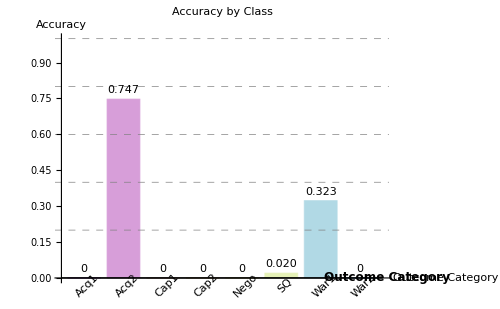
```mathematica
{{"Confusion Matrix Analysis"}, {}, {"Overall Accuracy: 0.187 (108/579)"}, {}, {}, {}, {-Graphics-}, {}, {"Detailed Breakdown"}, {{{"Category", "Actual Count", "Predicted Count", "Correct", "Accuracy"}, {"Acq1", 6, 10, 0, "0"}, {"Acq2", 99, 367, 74, "0.747"}, {"Cap1", 56, 0, 0, "0"}, {"Cap2", 99, 0, 0, "0"}, {"Nego", 99, 1, 0, "0"}, {"SQ", 99, 17, 2, "0.020"}, {"War1", 99, 184, 32, "0.323"}, {"War2", 22, 0, 0, "0"}}}, {}, {{{"Total Predictions:", 579}, {"Correct Predictions:", 108}, {"Error Rate:", "0.813"}, {"Number of Classes:", 8}}}}
```

```mathematica
table=CreateMetricsTable[result]
```

Outcome | Support | Precision | Recall | F1-Score
Acq1 | 6 | 0.000 | 0.000 | 0
Acq2 | 99 | 0.200 | 0.700 | 0.300
Cap1 | 56 | 0 | 0.000 | 0
Cap2 | 99 | 0 | 0.000 | 0
Nego | 99 | 0.000 | 0.000 | 0
SQ | 99 | 0.100 | 0.020 | 0.030
War1 | 99 | 0.200 | 0.300 | 0.200
War2 | 22 | 0 | 0.000 | 0
 |  |  |  | 
Macro Avg |  | 0.060 | 0.100 | 0.070
Weighted Avg |  |  |  | 0.100
Overall Accuracy |  |  |  | 0.200